```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
pris=Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
RandomSample[{imp11,imp2,imp,imp5,imp10,imp14,imp7,imp7,imp,imp4,imp,imp,imp,imp,imp14,imp,imp,imp3,imp,imp,imp13,imp,imp8,imp5,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp3,imp,imp,imp10,imp,imp13,imp12,imp,imp,imp10,imp,imp2,imp,imp,imp,imp8,imp4,imp3,imp,imp,imp4,imp1,imp,imp,imp,imp,imp1,imp9,imp,imp,imp9,imp,imp,imp,imp,imp11,imp,imp9,imp,imp,imp6,imp,imp2,imp,imp11,imp13,imp14,imp,imp5,imp,imp1,imp8,imp,imp,imp,imp12,imp,imp6,imp,imp,imp,imp6}]
```

{imp,imp2,imp,imp,imp,imp,imp,imp,imp8,imp,imp,imp,imp3,imp1,imp,imp14,imp2,imp,imp,imp10,imp,imp3,imp8,imp,imp12,imp,imp,imp,imp5,imp11,imp,imp6,imp,imp,imp,imp,imp,imp7,imp,imp3,imp14,imp8,imp6,imp6,imp1,imp,imp,imp,imp,imp12,imp,imp,imp9,imp,imp5,imp,imp9,imp12,imp,imp,imp,imp13,imp10,imp10,imp13,imp7,imp,imp11,imp9,imp,imp1,imp,imp,imp,imp11,imp,imp,imp7,imp,imp13,imp,imp4,imp,imp,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp14,imp2,imp,imp5,imp,imp4,imp}

```mathematica
m[ϵ1_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
lista={{imp13,imp,imp1,imp,imp2,imp12,imp,imp6,imp,imp1,imp12,imp9,imp6,imp4,imp10,imp,imp,imp6,imp4,imp,imp3,imp8,imp,imp10,imp14,imp13,imp14,imp5,imp,imp,imp11,imp,imp,imp7,imp,imp13,imp8,imp2,imp3,imp7,imp3,imp,imp12,imp,imp,imp1,imp,imp5,imp12,imp,imp11,imp2,imp,imp,imp,imp,imp5,imp14,imp11,imp,imp,imp,imp,imp5,imp9,imp,imp4,imp,imp7,imp14,imp3,imp,imp,imp,imp,imp,imp7,imp,imp,imp8,imp,imp,imp2,imp8,imp,imp,imp6,imp,imp13,imp9,imp9,imp1,imp,imp4,imp,imp11,imp,imp,imp10,imp10}};tra:=Module[{},
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
Table[{ω,tra},{ω,Range[0,3.1,0.01]}]]
```

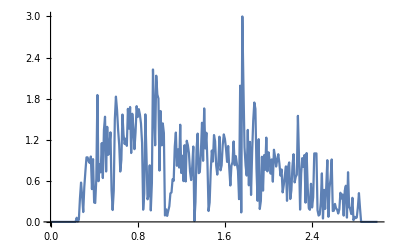

```mathematica
ListLinePlot[m[0.5]]
```

```mathematica
m5=Table[m[0.5],100]
```

{{{0.,2.8×10^-7},{0.01,1.95074×10^-7},{0.02,2.33346×10^-7},{0.03,2.06469×10^-7},{0.04,2.86046×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},278,{2.9,8.13461×10^-7},{2.91,5.81203×10^-7},{2.92,4.38906×10^-7},{2.93,3.43114×10^-7},{2.94,2.75197×10^-7},{2.95,2.25291×10^-7},{2.96,1.87593×10^-7},{2.97,1.58467×10^-7},{2.98,1.35531×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},98,{1}}
 |  |  |  |

```mathematica
Export["3impconfig.dat",%24]
```

3impconfig.dat

```mathematica
υ[n_,x_,y_]:=Module[{},
ρ1:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/1imp/1imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/2imp/2imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/3imp/3imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/4imp/4imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/5imp/5imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/6imp/6imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/7imp/7imp5.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[n]][[1;;300]][[;;,1]],100(m5[[n]][[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^1}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
{(*ListLinePlot[m5],ρ1,*)ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10(*,ρ11*)(*,list*)}]
```

```mathematica
Abs[υ[15,1.5,0]]
```

{0.584404,0.27113,0.0750411,0.0561448,0.151473,0.217193,0.245292,0.332668,0.358451}

```mathematica
aa=Join[Table[Table[Abs[υ[n,x,0.25]],{n,100}],{x,Range[0.251,0.4,0.01]}],Table[Table[Abs[υ[n,x,0.25]],{n,100}],{x,Range[0.41,2.99,0.05]}]]
```

{{{0.490354,0.257356,0.150626,0.0847866,0.0521247,0.0394427,0.0429685,0.0244305,0.0215701},98,{0.364114,0.131116,6,0.10467}},66}
 |  |  |  |

```mathematica
Dimensions[aa]
```

{67,100,9}

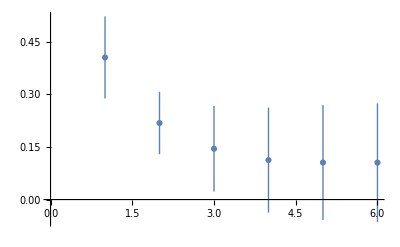
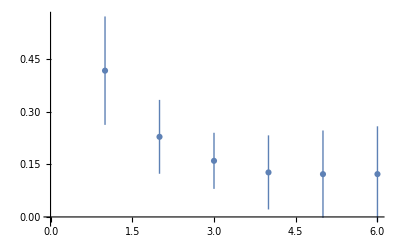
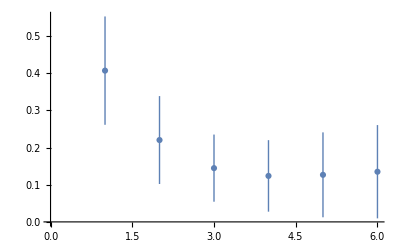
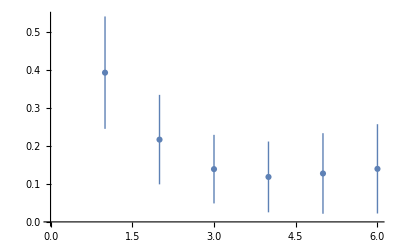
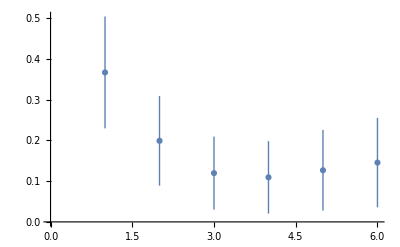
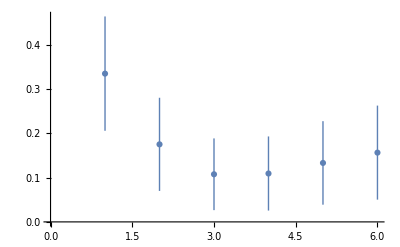
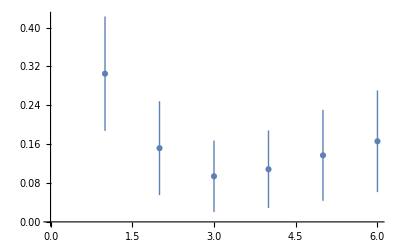
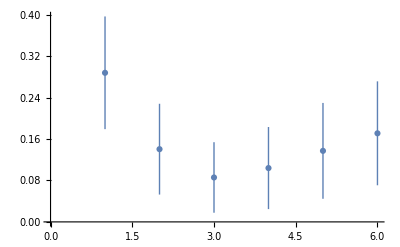

```mathematica
Table[ListPlot[Table[Around[Table[aa[[z]][[x]][[y]],{x,100}]],{y,6}]],{z,Dimensions[aa][[1]]}]
```

```mathematica
Mean[Table[Abs[(3-Table[Position[aa[[10]][[x]],Min[aa[[10]][[x]]]][[1,1]],{x,100}][[p]])]/3,{p,100}]]
```

1/3

```mathematica
Table[Mean[Table[Abs[(3-Table[Position[aa[[z]][[x]],Min[aa[[z]][[x]]]][[1,1]],{x,100}][[p]])]/3,{p,100}]],{z,15}]
```

{57/50,313/300,23/30,52/75,169/300,47/100,121/300,1/3,107/300,1/3,91/300,17/60,22/75,83/300,83/300}

```mathematica
Range[0.01,0.115,0.11/15]
```

{0.01,0.0173333,0.0246667,0.032,0.0393333,0.0466667,0.054,0.0613333,0.0686667,0.076,0.0833333,0.0906667,0.098,0.105333,0.112667}

```mathematica
Transpose[Join[{%174},{%176}]]
```

{{0.01,57/50},{0.0173333,313/300},{0.0246667,23/30},{0.032,52/75},{0.0393333,169/300},{0.0466667,47/100},{0.054,121/300},{0.0613333,1/3},{0.0686667,107/300},{0.076,1/3},{0.0833333,91/300},{0.0906667,17/60},{0.098,22/75},{0.105333,83/300},{0.112667,83/300}}

```mathematica
Dimensions[%174]
```

{15}

```mathematica
Table[Mean[Table[Abs[(3-Table[Position[aa[[z]][[x]],Min[aa[[z]][[x]]]][[1,1]],{x,100}][[p]])]/3,{p,100}]],{z,16,67}]
```

{19/75,4/15,29/150,29/150,4/25,3/20,13/100,1/10,29/300,13/150,13/150,8/75,8/75,11/100,31/300,13/150,3/50,7/150,11/300,2/75,7/300,7/300,1/50,1/50,1/50,1/75,1/100,1/75,1/75,1/100,1/150,1/150,1/300,1/300,1/150,1/150,1/150,1/150,1/300,1/300,1/300,1/300,1/100,1/150,1/150,1/300,1/300,1/300,1/300,1/150,1/100,1/100}

```mathematica
Range[0.4,2.99,0.05]
```

{0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95}

```mathematica
Join[%178,Transpose[Join[{Range[0.4,2.99,0.05]/3},{%155}]]]
```

```mathematica
{{0.01,57/50},{0.017333333333333333,313/300},{0.024666666666666667,23/30},{0.032,52/75},{0.03933333333333333,169/300},{0.04666666666666667,47/100},{0.054,121/300},{0.06133333333333334,1/3},{0.06866666666666667,107/300},{0.076,1/3},{0.08333333333333333,91/300},{0.09066666666666666,17/60},{0.09799999999999999,22/75},{0.10533333333333332,83/300},{0.11266666666666666,83/300},{0.13333333333333333,19/75},{0.15,4/15},{0.16666666666666666,29/150},{0.18333333333333335,29/150},{0.2,4/25},{0.21666666666666667,3/20},{0.23333333333333334,13/100},{0.25,1/10},{0.26666666666666666,29/300},{0.2833333333333333,13/150},{0.3,13/150},{0.31666666666666665,8/75},{0.3333333333333333,8/75},{0.35,11/100},{0.3666666666666667,31/300},{0.3833333333333333,13/150},{0.4,3/50},{0.41666666666666663,7/150},{0.43333333333333335,11/300},{0.45,2/75},{0.4666666666666666,7/300},{0.4833333333333334,7/300},{0.5,1/50},{0.5166666666666667,1/50},{0.5333333333333333,1/50},{0.5499999999999999,1/75},{0.5666666666666667,1/100},{0.5833333333333333,1/75},{0.6000000000000001,1/75},{0.6166666666666667,1/100},{0.6333333333333333,1/150},{0.65,1/150},{0.6666666666666666,1/300},{0.6833333333333333,1/300},{0.7,1/150},{0.7166666666666666,1/150},{0.7333333333333334,1/150},{0.75,1/150},{0.7666666666666667,1/300},{0.7833333333333333,1/300},{0.7999999999999999,1/300},{0.8166666666666667,1/300},{0.8333333333333333,1/100},{0.8499999999999999,1/150},{0.8666666666666667,1/150},{0.8833333333333333,1/300},{0.9,1/300},{0.9166666666666666,1/300},{0.9333333333333333,1/300},{0.95,1/150},{0.9666666666666666,1/100},{0.9833333333333334,1/100}}
```

{{0.01,57/50},{0.0173333,313/300},{0.0246667,23/30},{0.032,52/75},{0.0393333,169/300},{0.0466667,47/100},{0.054,121/300},{0.0613333,1/3},{0.0686667,107/300},{0.076,1/3},{0.0833333,91/300},{0.0906667,17/60},{0.098,22/75},{0.105333,83/300},{0.112667,83/300},{0.133333,19/75},{0.15,4/15},{0.166667,29/150},{0.183333,29/150},{0.2,4/25},{0.216667,3/20},{0.233333,13/100},{0.25,1/10},{0.266667,29/300},{0.283333,13/150},{0.3,13/150},{0.316667,8/75},{0.333333,8/75},{0.35,11/100},{0.366667,31/300},{0.383333,13/150},{0.4,3/50},{0.416667,7/150},{0.433333,11/300},{0.45,2/75},{0.466667,7/300},{0.483333,7/300},{0.5,1/50},{0.516667,1/50},{0.533333,1/50},{0.55,1/75},{0.566667,1/100},{0.583333,1/75},{0.6,1/75},{0.616667,1/100},{0.633333,1/150},{0.65,1/150},{0.666667,1/300},{0.683333,1/300},{0.7,1/150},{0.716667,1/150},{0.733333,1/150},{0.75,1/150},{0.766667,1/300},{0.783333,1/300},{0.8,1/300},{0.816667,1/300},{0.833333,1/100},{0.85,1/150},{0.866667,1/150},{0.883333,1/300},{0.9,1/300},{0.916667,1/300},{0.933333,1/300},{0.95,1/150},{0.966667,1/100},{0.983333,1/100}}

```mathematica
Interpolation[%135,InterpolationOrder->4]
```

InterpolatingFunction[…]

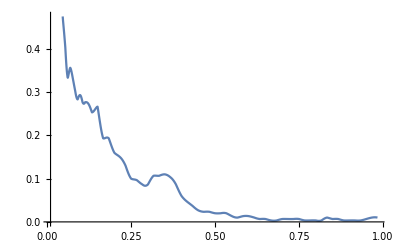

```mathematica
Plot[%143[x],{x,0.01,0.9833333333333334}]
```

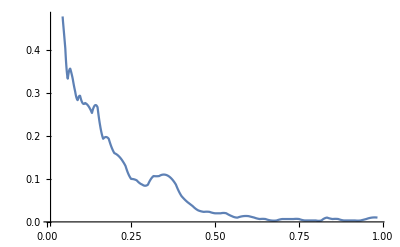

```mathematica
Plot[%141[x],{x,0.01,0.9833333333333334}]
```

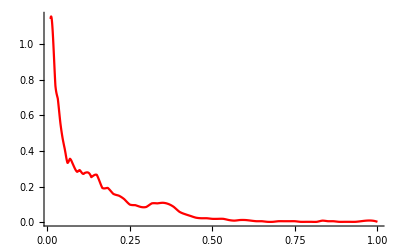

```mathematica
Plot[%136[x],{x,0.01,1},PlotRange->All,PlotStyle->Red]
```

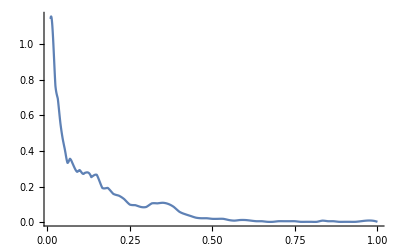

```mathematica
Plot[%180[x],{x,0.01,1.0},PlotRange->All]
```

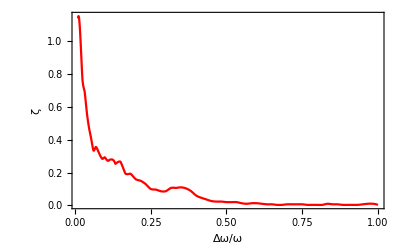

```mathematica
Show[%145,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{HoldForm[ζ],None},{HoldForm[Δω/ω],None}},LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},Frame->True,(*Epilog->{Text[Style["(b)","Times New Roman",18],{0.2,2.8}]},*)PlotStyle->{Black,Dashed}]
```

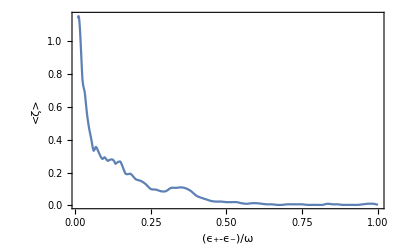

```mathematica
Show[%184,FrameLabel->{{RawBoxes[RowBox[{TagBox[RowBox[{"<","ζ"}],HoldForm],">"}]],None},{HoldForm[(SubPlus[ϵ]-SubMinus[ϵ])/ω],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%189,PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]}]
```

-Graphics-

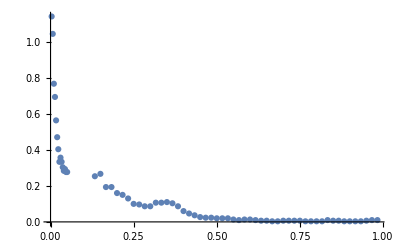

```mathematica
ListPlot[%160,PlotRange->All]
```

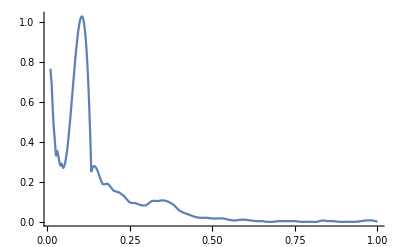

```mathematica
Plot[%161[x],{x,0.01,1},PlotRange->All]
```

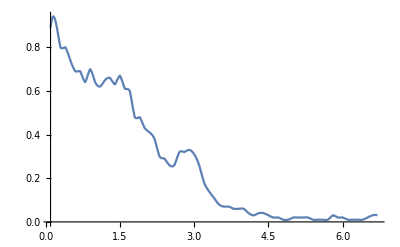

```mathematica
Plot[%122[x],{x,1/10,67/10}]
```

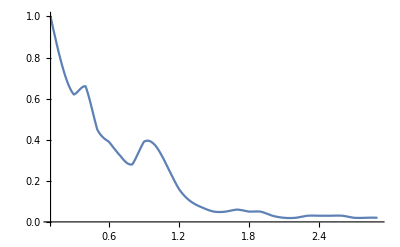

```mathematica
Plot[%46[x],{x,1/10,29/10}]
```

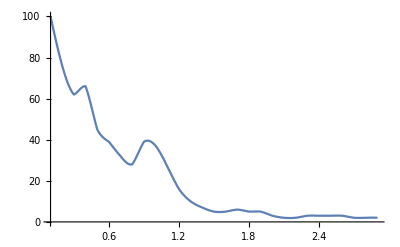

```mathematica
Plot[%43[x],{x,1/10,29/10}]
```

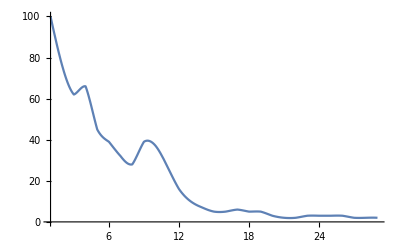

```mathematica
Plot[%39[x],{x,1,29}]
```

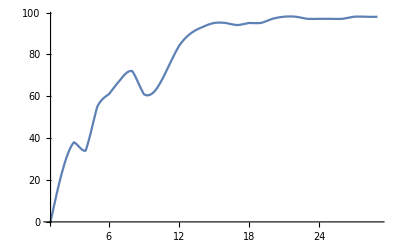

```mathematica
Plot[%36[x],{x,1,29}]
```

{{0.0719266,0.01045,0.00366185,0.00188542,0.00154209,0.00108814,0.00164236,0.000283958,0.0000974813},{0.107902,0.0580049,0.0545028,0.0669608,0.0794526,0.0937426,0.096606,0.148191,0.160445},{0.201892,0.124977,0.0900777,0.0868255,0.111838,0.138098,0.149608,0.187587,0.203626},{0.336196,0.190954,0.159313,0.152525,0.153552,0.149282,0.156896,0.183207,0.192311},{0.280919,0.165907,0.143063,0.157484,0.180254,0.209479,0.230267,0.292197,0.314814},{0.340128,0.175514,0.128645,0.127486,0.145207,0.169146,0.176613,0.242487,0.266764},{0.233889,0.10964,0.0860252,0.105718,0.139744,0.178976,0.200483,0.301555,0.342913},{0.411462,0.235999,0.196818,0.207261,0.239459,0.277399,0.29683,0.392015,0.431303},{0.48585,0.239441,0.177629,0.182775,0.214801,0.259421,0.280219,0.405456,0.447756},{0.256327,0.0793837,0.0945338,0.159088,0.231927,0.300634,0.321902,0.480671,0.527537},{0.439105,0.169558,0.142528,0.183642,0.243279,0.300143,0.316626,0.442725,0.478522},{0.405059,0.179672,0.198689,0.278419,0.368834,0.451397,0.475727,0.648903,0.696423},{0.505727,0.168107,0.113958,0.14877,0.209102,0.271713,0.297086,0.424932,0.464448},{0.520643,0.188876,0.160839,0.219488,0.299885,0.376161,0.406904,0.541062,0.582757},{0.662449,0.244446,0.160029,0.182656,0.238672,0.294156,0.320993,0.423946,0.461275},{0.505357,0.156744,0.133593,0.195588,0.275589,0.349134,0.378819,0.503777,0.543203},{0.492952,0.161332,0.132853,0.187127,0.26162,0.331389,0.360068,0.477298,0.514878},{0.608603,0.213903,0.151212,0.185537,0.248382,0.312776,0.338218,0.436558,0.470625},{0.618913,0.237595,0.169094,0.198236,0.256409,0.316676,0.340475,0.436924,0.470349},{0.538788,0.196347,0.16051,0.21109,0.286033,0.357783,0.394646,0.499967,0.538346},{0.602559,0.213217,0.137962,0.159128,0.211677,0.268415,0.3023,0.381743,0.416151},{0.584252,0.208013,0.138553,0.162551,0.215872,0.272684,0.306002,0.382476,0.416034},{0.536542,0.18511,0.131766,0.165629,0.227514,0.286889,0.302501,0.383996,0.41315},{0.556925,0.220237,0.162536,0.192967,0.253521,0.313022,0.317879,0.418874,0.450509},{0.427983,0.187455,0.188518,0.256819,0.340691,0.4151,0.42791,0.528583,0.563922},{0.548574,0.202666,0.134389,0.150001,0.195209,0.242358,0.246524,0.318955,0.344396},{0.552909,0.217415,0.14699,0.162563,0.208228,0.254663,0.265212,0.335883,0.359152},{0.549908,0.2148,0.144475,0.157063,0.198249,0.241508,0.247972,0.318728,0.342536}}

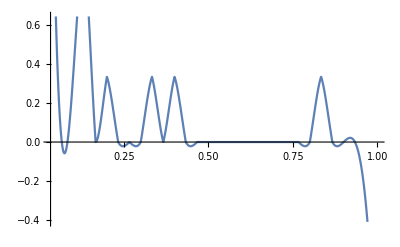

```mathematica
rr=Table[υ[RandomInteger[{1,100}],x,00.24],{x,Range[0.241,2.98,0.1]}]
Plot[Interpolation[Table[{x/30,Abs[Position[rr[[x]],Min[rr[[x]]]][[1,1]]*14-3*14]/(3*14)},{x,28}]][x],{x,1/30,30/30}]
```

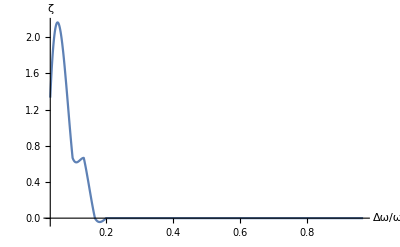

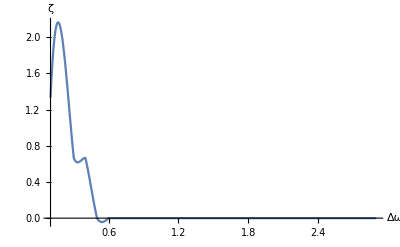

```mathematica
Show[%67,AxesLabel->{HoldForm[Δω/ω],HoldForm[ζ]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

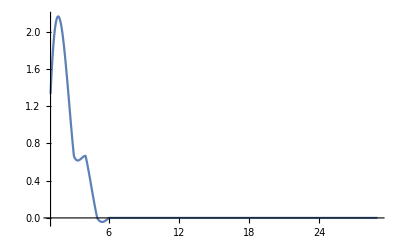

```mathematica
Plot[%58[x],{x,1,29}]
```

```mathematica
Table[{z/10,(100-Count[Flatten[Table[Position[aa[[z]][[x]],Min[aa[[z]][[x]]]],{x,100}]],3])/100},{z,Dimensions[aa][[1]]}]
```

```mathematica
rr=Table[υ[RandomInteger[{1,100}],x,00.24],{x,Range[0.241,2.98,0.1]}]
Plot[Interpolation[Table[{x/30,Abs[Position[rr[[x]],Min[rr[[x]]]][[1,1]]*14-3*14]/(3*14)},{x,28}]][x],{x,1/30,30/30}]
```